R1 = 0.04

T1 = 0.96

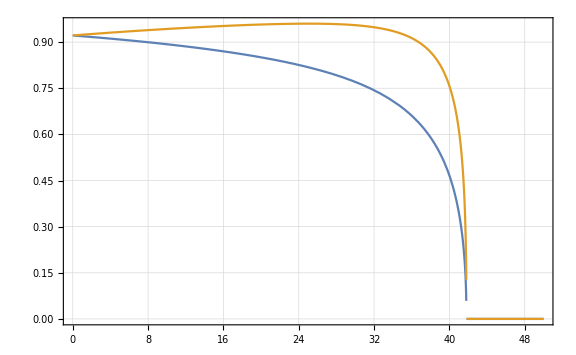

angle = 40, ts = 0.466238, tp = 0.757546

angle = 0, ts = 0.9216, tp = 0.9216

angle = 7, ts = 0.902652, tp = 0.93701

```mathematica
ClearAll["Global`*"];

(* Vacuum *)
n0=1;

(* Glass *)
n1=1.5;

n2=1;

(* First boundary *)
r1=(n0-n1)^2/(n0+n1)^2;
t1=4*n0*n1/(n0+n1)^2;

Print["R1 = ", r1];
Print["T1 = ", t1];

(* =================== *)

rs[a_]:=Abs[(n1*Cos[a]-n2*Sqrt[1-((n1/n2)*Sin[a])])/(n1*Cos[a]+n2*Sqrt[1-((n1/n2)*Sin[a])])]^2;
rp[a_]:=Abs[(n1*Sqrt[1-((n1/n2)*Sin[a])]-n2*Cos[a])/(n1*Sqrt[1-((n1/n2)*Sin[a])]+n2*Cos[a])]^2;

ts[a_]:=t1*(1-rs[a]);
tp[a_]:=t1*(1-rp[a]);

Print[Plot[{ts[x Degree],tp[x Degree]},{x,0,50}, PlotRange->All, Frame -> True, GridLines -> Automatic, ImageSize->Large]];

angle =40;
Print["angle = ", angle, ", ts = ", ts[angle Degree], ", tp = ", tp[angle Degree]];

angle =0;
Print["angle = ", angle, ", ts = ", ts[angle Degree], ", tp = ", tp[angle Degree]];

angle =7;
Print["angle = ", angle, ", ts = ", ts[angle Degree], ", tp = ", tp[angle Degree]];
```